```mathematica
SetDirectory[NotebookDirectory[]];

a=Sound[SoundNote["C"]];

b= AudioLocalMeasurements[a, {"SpectralRollOff"}]
```

TimeSeries[…]

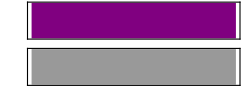

```mathematica
a
```

```mathematica
Median[b]
```

527.563

```mathematica
(*Valore atteso: 524, buon risultato*)
```

```mathematica
chiave = Import["../immagini/chiave.png"]
```

-Graphics-

```mathematica
nota = Import["../immagini/nota_senza_barra.png"]
```

-Graphics-

```mathematica
ImageCompose[chiave, nota, {30, 287}]
(*397 -> sol 
12.75 ogni nota
   409.5 -> la
422 -> si 
355 D4

CIRCA 12.75 ogni nota

ecc...*)
```

-Graphics-

```mathematica
Options[AudioCapture]
```

{Appearance→Automatic,AudioChannelAssignment→Automatic,AudioInputDevice→Automatic,AudioLabel→Automatic,AudioOutputDevice→Automatic,CaptureRunning→Automatic,MaxDuration→None,MetaInformation→<||>,OverwriteTarget→False,SampleRate→Automatic,SoundVolume→1}

```mathematica
?Module
Head[{}]
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

```mathematica
NoteDistance[a_, b_:"C4"] := 12FromDigits[StringTake[a, -1]]- 12FromDigits[StringTake[b, -1]] +Position[{"C","C#", "D", "D#",  "E", "F", "F#", "G", "G#",  "A", "A#",  "B"}, StringTake[a, 1]][[1]][[1]]- Position[{"C","C#", "D", "D#",  "E", "F", "F#", "G", "G#",  "A", "A#",  "B"}, StringTake[b, 1]][[1]][[1]]+
If[StringContainsQ[a, "#"], 1, 0]+If[StringContainsQ[b, "#"], -1, 0];
```

```mathematica
NoteSpaces[a_, b_:"C4"] := 7FromDigits[StringTake[a, -1]]- 7FromDigits[StringTake[b, -1]] +Position[{"C", "D","E", "F", "G","A","B"}, StringTake[a, 1]][[1]][[1]]- Position[{"C","D","E", "F","G","A", "B"}, StringTake[b, 1]][[1]][[1]];
```

```mathematica
NotePreorderQ[a_, b_:"C4"] := NoteDistance[a, b]≤0;
```

```mathematica
NoteSpacesPreorderQ[a_, b_:"C4"] := NoteSpaces[a, b]≤0;
ClearAll[PrintNote]
```

```mathematica
Module[{chiave, nota, notaBarra, barra},

chiave = Import["../immagini/chiave.png"];
nota = Import["../immagini/nota_senza_barra.png"];
notaBarra = Import["../immagini/nota_barra.png"];
barra = Import["../immagini/barra.png"];

PrintNote[o_, n_/;NotePreorderQ[n, "G5"]&& !NotePreorderQ[n,"C4"], back_:chiave]:=ImageCompose[back, nota,  {300+100*o,355+13.2*NoteSpaces[n, "D4"] }];
PrintNote[ o_, n_/;NotePreorderQ[n, "B3"]&& !NotePreorderQ[n,"E2"], back_:chiave]:=ImageCompose[back, nota, {300+100*o,87+13.2*NoteSpaces[n, "F2"] }];
PrintNote[ o_, n_/;NotePreorderQ[n, "C4"]&& NotePreorderQ["C4",n], back_:chiave]:=ImageCompose[back, notaBarra, {300+100*o,287}];

PrintNote[o_, n_/;NotePreorderQ["A5", n]&&Mod[NoteSpaces[n, "G5"], 2]==1, back_:chiave]:=FoldList[
ImageCompose[#1, barra,  {300+100*o,473.8+13.2*#2 }]&,
ImageCompose[back, notaBarra,  {300+100*o,355+13.2*NoteSpaces[n, "D4"] }],
Range[2, NoteSpaces[n, "F5"]-2, 2]][[-1]];

PrintNote[o_, n_/;NotePreorderQ["A5", n]&&Mod[NoteSpaces[n, "G5"], 2]==0, back_:chiave]:=FoldList[
ImageCompose[#1, barra,  {300+100*o,473.8+13.2*#2 }]&,
ImageCompose[back, nota,  {300+100*o,355+13.2*NoteSpaces[n, "D4"] }],
Range[2, NoteSpaces[n, "F5"], 2]][[-1]];

PrintNote[o_, n_/;NotePreorderQ[n, "F2"]&&Mod[NoteSpaces[n, "F2"], 2]==1, back_:chiave]:=FoldList[
ImageCompose[#1, barra,  {300+100*o,87-13.2*(#2-1) }]&,
ImageCompose[back, notaBarra,  {300+100*o,87-13.2*NoteSpaces["F2", n] }],
Range[2, NoteSpaces["F2", n], 2]][[-1]];

PrintNote[o_, n_/;NotePreorderQ[n, "F2"]&&Mod[NoteSpaces[n, "F2"], 2]==0, back_:chiave]:=FoldList[
ImageCompose[#1, barra,  {300+100*o,87-13.2*(#2-1) }]&,
ImageCompose[back, nota,  {300+100*o,87-13.2*NoteSpaces["F2", n] }],
Range[2, NoteSpaces["F2", n], 2]][[-1]];

PrintChord[o_, c_, back_:chiave] :=Fold[PrintNote[o, #2, #1]&, back, c];
PrintMelody[m_, back_:chiave] := Fold[PrintChord[#2, #1]&, back, Fold[{}];
]
```

```mathematica
{1,2 }{3,4}
```

{3,8}

```mathematica
NotePreorderQ["A5", "A5"]&&Mod[NoteSpaces["A5", "G5"], 2]==1
```

True

```mathematica
Range[0, NoteSpaces["F5", "E6"], 2]
```

```mathematica
NoteSpaces["D4", "F5"]
```

-9

```mathematica
Range[0, NoteSpaces["F2", "C2"], 2]
```

{0,2}

```mathematica
PrintNote[0, "C2"]
```

-Graphics-

```mathematica
PrintChord[0, {"C4", "E4", "G4", "B5"}]
```

-Graphics-

```mathematica
PrintMelody[{{"C4", "E4", "G4"}, {"D4", "F4", "A4"}}]
```

Fold::normal: Nonatomic expression expected at position 3 in ….

StringTake::strse: String or list of strings expected at position 1 in StringTake[PrintNote[{C4,E4,G4},#2,#1]&,-1].

FromDigits::nlst: The expression StringTake[PrintNote[{C4,E4,G4},#2,#1]&,-1] is not a list of digits or a string of valid digits.

StringTake::strse: String or list of strings expected at position 1 in StringTake[PrintNote[{C4,E4,G4},#2,#1]&,1].

Part::partw: Part 1 of {} does not exist.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[PrintNote[{C4,E4,G4},#2,#1]&,#].

StringTake::strse: String or list of strings expected at position 1 in StringTake[PrintNote[{C4,E4,G4},#2,#1]&,-1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringTake[PrintNote[{C4,E4,G4},#2,#1]&,-1] is not a list of digits or a string of valid digits.

Part::partw: Part 1 of {} does not exist.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[PrintNote[{C4,E4,G4},#2,#1]&,#].

FromDigits::nlst: The expression StringTake[PrintNote[{C4,E4,G4},#2,#1]&,-1] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[PrintNote[{C4,E4,G4},#2,#1]&,#].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

PrintNote[{D4,F4,A4},-Graphics-,PrintNote[{D4,F4,A4},-Graphics-,PrintNote[{D4,F4,A4},PrintNote[{C4,E4,G4},#2,#1]&,-Graphics-]]]